```mathematica
<<xlr8r.m;
<<Cellzilla2D.m;
```

xCellerator 0.90 (2-Nov-2012) loaded Thu 8 Nov 2012 17:46:40
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Thu 8 Nov 2012 17:46:40
using xCellerator 0.90 and XSSA 1204002

## AddCell-Example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
w=RandomizeTemplate[TemplateRectangular[{0,10,2}, {0,10,2}], .02];
```

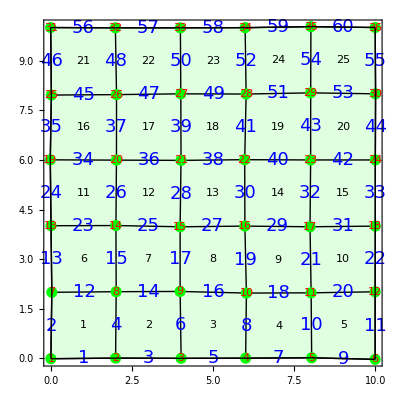

```mathematica
ShowTissue[w, Frame-> True, "Vertices"-> {Directive[Green,PointSize[.02]]},"VertexNumbers"-> {Directive[Red, FontSize-> 18]}, 
"EdgeNumbers"-> True, 
"EdgeNumberStyle"-> Directive[Blue, FontSize-> 18, FontFamily-> "Arial"],  "CellNumbers"-> True]
```

```mathematica
p=NTissueVertices[w]
```

36

```mathematica
q=NTissueEdges[w];
```

```mathematica
w1=AddVertex[w,{12.5, 0.25}];
w2=AddEdge[w1,{p+1,6}];
w3=AddEdge[w2, {p+1,12}];
w4=AddCell[w3, {q+1, q+2, 11}];
```

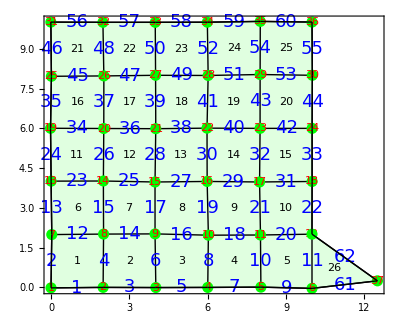

```mathematica
ShowTissue[w4, Frame-> True, "Vertices"-> {Directive[Green,PointSize[.02]]},"VertexNumbers"-> {Directive[Red, FontSize-> 18]}, 
"EdgeNumbers"-> True, 
"EdgeNumberStyle"-> Directive[Blue, FontSize-> 18, FontFamily-> "Arial"],  "CellNumbers"-> True]
```